# Basics of Mathematica

Complex  Numbers

This section will cover the basics of complex numbers. We will see the application  of complex numbers
to problems in physics and engineering. We will also do some basic plots involving imaginary numbers.

### Complex Expand

```mathematica
ComplexExpand[(x + I y)^2]
```

x^2+2 ⅈ x y-y^2

```mathematica
ComplexExpand[(x + I y)^2,{x, y}]
```

-Im[x]^2+Im[y]^2-2 Im[y] Re[x]+Re[x]^2-2 Im[x] Re[y]-Re[y]^2+ⅈ (-2 Im[x] Im[y]+2 Im[x] Re[x]-2 Im[y] Re[y]+2 Re[x] Re[y])

Note that  in the first case, x  and y  are treated as real numbers, eliminating the need
for producing the real and imaginary parts of, e.g. x2 . In the second case, x
 and y  are treated as complex numbers, each with its own real and imaginary
parts.

### An Example from Optics

#### Representation of Waves by Complex Numbers

For example, a wave which always  consists of amplitude and a phase, begs a representation by a complex 
number. Thus the sinusoidal wave

						 Acos(k * r −  ωt +  φ)

Can be thought of as the real part of  the complex wave

				                       Aei(k.r−ωt+φ) ≡  Ze^-iwt

where Z  is the complex amplitude Ae^(i(k.r+φ)).

```mathematica
1 - Cos[N[ GoldenRatio]] + I Sin[N[ GoldenRatio]]
```

1.04722+0.998885 ⅈ

```mathematica
2- 2 Cos[ϕ]
```

2-2 Cos[ϕ]

```mathematica
(1-Cos[N[ϕ]])/(1-Cos[ϕ])
```

1

#### The intensity of a five-slit arrangement

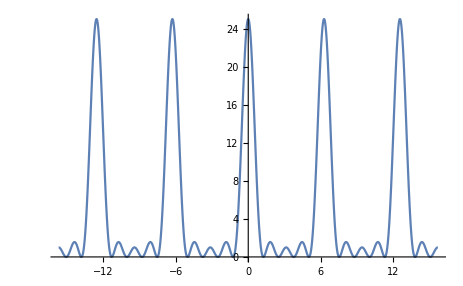

```mathematica
Plot[(1-Cos[N[5  ϕ]])/(1-Cos[ϕ]),{ϕ, -5 Pi,5 Pi},PlotRange->All]
```